#### Defs

```mathematica
(* Ξ will express elements of the algebra, NopQ checks if sth is an operator *)
NopQ[aa_]:=FreeQ[aa,Ξ]
```

```mathematica
a_\[Application]b_Plus:=Map[a\[Application]#&,b,{1}]
a_Plus\[Application]b_:=Map[#\[Application]b&,a,{1}]
(a_?NopQ b_)\[Application]c_:=a(b\[Application]c)
a_\[Application](b_?NopQ c_):=b(a\[Application]c)
a_\[Application]b_:=0/;a b===0
```

```mathematica
e.g.:
(w Ξ[a]+Ξ[b])\[Application](3Ξ[0]+Ξ[1])
```

3 w Ξ[a]\[Application]Ξ[0]+w Ξ[a]\[Application]Ξ[1]+3 Ξ[b]\[Application]Ξ[0]+Ξ[b]\[Application]Ξ[1]

```mathematica
(* Natural representation of any (…q)^n p^m… as Ξ[…,{n,0},{0,m},…] *)
Clear[Ξ]
Ξ[aa___,{0,0},bb___]:=Ξ[aa,bb]
Ξ[aa___,{mm_,0},{nn_,0},bb___]:=Ξ[aa,{mm+nn,0},bb]
Ξ[aa___,{0,mm_},{0,nn_},bb___]:=Ξ[aa,{0,mm+nn},bb]
Ξ/:Ξ[aa___]\[Application]Ξ[bb___]:=Ξ[aa,bb]
```

```mathematica
Format[Ξ[]]:=𝟙(*;Ξ[]=1;*)
Format[Ξ[aa__]]:=Row@Map[q^#⟦1⟧p^#⟦2⟧&,{aa}]
```

```mathematica
e.g.:
Ξ[{r,0}]\[Application]Ξ[]\[Application]Ξ[{3,0}]\[Application](2 Ξ[{1,0}]+Ξ[{0,2}])
```

2 q^(4+r)+q^(3+r)p^2

```mathematica
(* shorthand for symmetric product, commutator, q^n, p^m, 𝟙 *)
S[aa_,bb_]:=(aa\[Application]bb+bb\[Application]aa)/2
K[aa_,bb_]:=aa\[Application]bb-bb\[Application]aa
𝔔[nn_]:=Ξ[{nn,0}]
𝔓[mm_]:=Ξ[{0,mm}]
1=Ξ[];
```

```mathematica
(* represent q -> z and p -> -ⅈ∂_z *)
Clear[Ψ]
Ψ[{},oo_]:=oo
Ψ[{aa___,{bb1_,bb2_}},oo_]:=Ψ[{aa},If[bb1===0,(-ⅈ)^bb2 D[oo,{z,bb2}],z^bb1 oo]]
(*you can sepcify the wave function, φ[z] by default *)
derivify[AA_,ff:_:φ[z]]:=Collect[ReplaceRepeated[AA,{Ξ[aa___]:>Ψ[{aa},ff]}],{_[z],z}]
```

### Orderings

```mathematica
(* Symmetric q^n p^m separation *)
```

```mathematica
Clear[𝒮]
𝒮[nn_,mm_]:=S[Ξ[{nn,0}],Ξ[{0,mm}]]
```

```mathematica
(* naive Weyl order of q^nn p^mm*)
Clear[𝒲]
𝒲[nn_,0]:=Ξ[{nn,0}];
𝒲[0,mm_]:=Ξ[{0,mm}];
𝒲[nn_,mm_]:=(𝒲[nn,mm]=Collect[(mm S[𝒲[nn,mm-1],Ξ[{0,1}]]+nn S[𝒲[nn-1,mm],Ξ[{1,0}]])/(nn+mm),Ξ[___]])
```

```mathematica
e.g.:
𝒲[3,2]
```

(p^2q^3)/10+(q^3p^2)/10+(pq^3p)/10+(qp^2q^2)/10+(q^2p^2q)/10+pqpq^2/10+(pq^2pq)/10+(qpq^2p)/10+(q^2pqp)/10+qpqpq/10

```mathematica
(* reorder with all q to the left, making use of the (left-ordered-)commutator KL[n,m]=[q^n,p^m] = ⅈm∑_j q^(n-1-j)p^m q^j *)
Clear[KL,LeQ]
KL[1,1]=ⅈ Ξ[];
KL[nn_,mm_]:=0/;nn===0∨mm===0
KL[nn_,mm_]:=(KL[nn,mm]=ⅈ mm  LeQ@Sum[𝔔[nn-1-j]\[Application]𝔓[mm-1]\[Application]𝔔[j],{j,0,nn-1}])/;nn>1∨mm>1
LeQ[AA_]:=Collect[ReplaceRepeated[AA,{Ξ[aa___,{0,nn_},{mm_,0},bb___]:>Ξ[aa,{mm,0},{0,nn},bb]-Ξ[aa]\[Application]KL[mm,nn]\[Application]Ξ[bb]}],Ξ[___]]
```

```mathematica
𝒲[5,5]//Timing;
{%⟦1⟧,LeQ[%⟦2⟧]//Timing}
```

{0.173085,{0.123267,-(15 ⅈ 𝟙)/4+(75 qp)/2+75 ⅈ q^2p^2-50 q^3p^3-25/2 ⅈ q^4p^4+q^5p^5}}

```mathematica
(* Weyl order with all q on the left *)
Clear[WL]
WL[nn_,0]=Ξ[{nn,0}];
WL[0,mm_]=Ξ[{0,mm}];
WL[nn_,mm_]:=(WL[nn,mm]=Collect[LeQ[(mm S[WL[nn,mm-1],Ξ[{0,1}]]+nn S[WL[nn-1,mm],Ξ[{1,0}]])/(nn+mm)],Ξ[___]])
```

```mathematica
derivify@𝒲[9,5]//Timing
WL[9,5]//Timing
```

{10.7329,-945/2 ⅈ z^4 φ[z]-945 ⅈ z^5 φ'[z]-630 ⅈ z^6 φ''[z]-180 ⅈ z^7 φ^(3)[z]-45/2 ⅈ z^8 φ^(4)[z]-ⅈ z^9 φ^(5)[z]}

{0.023372,-(945 ⅈ q^4)/2+945 q^5p+630 ⅈ q^6p^2-180 q^7p^3-45/2 ⅈ q^8p^4+q^9p^5}

### Averages

```mathematica
Clear[Μ]
NopQ[Power[Μ[_],_.]]:=True
Μ[a_+b_]:=Μ[a]+Μ[b]
Μ[a_?NopQ b:_:Ξ[]]:=a Μ[b]
Μ[Ξ[]]:=1
```

```mathematica
Format[HoldPattern@Μ[a_]]:=⟨a⟩
```

```mathematica
Μ[𝒲[2,1]+Μ[𝔔[1]]𝔓[1]]
```

⟨p⟩ ⟨q⟩+⟨pq^2⟩/3+⟨q^2p⟩/3+⟨qpq⟩/3

```mathematica
Clear[CircPow];CircPow[aa_,0]:=Ξ[]
CircPow[aa_,nn_/;nn>0]:=aa\[Application]CircPow[aa,nn-1]
```

```mathematica
Clear[Var,meanShiftL]
meanShiftL[aa__]:=Map[CircPow[𝔔[1]-Μ[𝔔[1]] Ξ[],#⟦1⟧]\[Application]CircPow[𝔓[1]-Μ[𝔓[1]] Ξ[],#⟦2⟧]&,{aa}]
Var[nn_,mm_]:=Μ@Collect[𝒲[nn,mm]/.{Ξ[]:>0,Ξ[aa__]:>Fold[#1\[Application]#2&,meanShiftL[aa]]},Ξ[___]]
```

```mathematica
𝒲[1,2]//LeQ
Var[1,2]//LeQ//Simplify
Var[2,0]
```

-ⅈ p+qp^2

2 ⟨p⟩^2 ⟨q⟩-⟨p^2⟩ ⟨q⟩-2 ⟨p⟩ ⟨qp⟩+⟨qp^2⟩

-⟨q⟩^2+⟨q^2⟩

### System

```mathematica
(*Specific dynamical system *)
```

```mathematica
ℋ=1/2 𝔓[2]+1/2 𝔔[2]0+1/nn 𝔔[nn]/.nn->4
{dQ,dP}=LeQ@{-ⅈ K[𝔔[1],ℋ],-ⅈ K[𝔓[1],ℋ]}
```

p^2/2+q^4/4

{p,-q^3}

```mathematica
(* Duffing *)
{dQ1,dP1}={𝔓[1],-𝔔[1]-𝔔[3]-𝔓[1]}
K[dQ1,𝔓[1]]+K[𝔔[1],dP1]
```

{p,-p-q-q^3}

pq-qp

```mathematica
(* derivation on Ξ by Leibniz *)
Clear[dX];dX[]=0;
dX[{nn_,0}]:=(dX[{nn,0}]=Collect[Sum[𝔔[j-1]\[Application]dQ\[Application]𝔔[nn-j],{j,1,nn}],Ξ[___]])
dX[{0,mm_}]:=(dX[{0,mm}]=Collect[Sum[𝔓[j-1]\[Application]dP\[Application]𝔓[mm-j],{j,1,mm}],Ξ[___]])
dX[{nn_,mm_},bb__]:=(dX[{nn,mm}]\[Application]Ξ[bb]+Ξ[{nn,mm}]\[Application]dX[bb])
```

```mathematica
Clear[dW];dW[nn_,mm_]:=(dW[nn,mm]=Collect[LeQ[WL[nn,mm]/.Ξ->dX],Ξ[___]])
Clear[dS];dS[nn_,mm_]:=(dS[nn,mm]=Collect[𝒮[nn,mm]/.Ξ->dX,Ξ[___]])
```

#### Derivatives of means

```mathematica
derM[AA_]:=Module[{Γ={},dΓ},
AA/.Μ[H:Ξ[xx__]]:>(AppendTo[Γ,H];Μ[H]);
dΓ=(Μ/@DeleteDuplicates[Γ])/.Ξ->dX;
Collect[D[AA,{Γ}].(dΓ),Ξ[___]]
]
```

```mathematica
𝒲[2,1]/.Ξ->dX//Simplify
```

-q^5+2/3 (p^2q+qp^2+pqp)

```mathematica
derM@Μ[𝒲[2,1]]
%-(-1) Μ[𝒲[5,0]]-2 Μ[𝒲[1,2]]//Simplify
derM@Var[2,0]-2Var[1,1]//Simplify
```

1/3 (-⟨q^5⟩+⟨p^2q⟩+⟨qp^2⟩)+1/3 (-⟨q^5⟩+⟨p^2q⟩+⟨pqp⟩)+1/3 (-⟨q^5⟩+⟨qp^2⟩+⟨pqp⟩)

0

0

## Decompositions

```mathematica
Clear[pru];pru[0]={{0,0}};
pru[{nn_,mm_}]:={}/;(nn<0∨mm<0)
pru[{nn_,mm_}]:=(pru[{nn,mm}]={{nn,mm}}~Join~pru[{nn-2,mm-2}])/;nn≥0∧mm≥0
Clear[decompose];
decompose=W↦Module[{Γ={},L,dW,cfs={},sol,t0,t1,t2,t3},
(*t0=AbsoluteTime[];*)
dW=LeQ[W]/.Ξ[a___]:>(Γ=Γ∪pru[Plus[a]];Ξ[a]);
(*Print["prefab: ",(t1=AbsoluteTime[])-t0];*)
Collect[dW-LeQ@Sum[(L@@pp)(𝒮@@pp),{pp,Γ}],Ξ[___],(AppendTo[cfs,#];0)&];
(*Print["collect: ",(t2=AbsoluteTime[])-t1];*)
sol=Solve[cfs==0];
(*Print["solvd: ",(t3=AbsoluteTime[])-t2];*)
Sum[(L@@pp)(𝔖@@pp),{pp,Γ}]/.sol⟦1⟧];
```

```mathematica
Clear[sru];sru[{0,0}]:={{0,0}};
sru[{nn_,mm_}]:={}/;(nn<0∨mm<0)
sru[{nn_,mm_}]:=(sru[{nn,mm}]={{nn,mm}}~Join~sru[{nn-1,mm-1}])/;nn≥0∧mm≥0
Clear[kompost];
kompost=W↦Module[{Γ={},L,dW,k,sol},
dW=derivify[W,Exp[k z]]/Exp[k z];(*Print[Expand@dW/.{k->κ}];*)
Expand[z k dW]/.{z^a_. k^b_.:>(Γ=Γ∪sru[{a-1,b-1}];0)};(*Print["Γ = ",Γᵀ//MatrixForm];*)
sol=SolveAlways[Expand[dW-derivify[Sum[(L@@pp)(WL@@pp),{pp,Γ}],Exp[k z]]/Exp[k z]]==0,{z,k}];
Sum[(L@@pp)(𝔚@@pp),{pp,Γ}]/.sol⟦1⟧];
```

```mathematica
decompose[𝔓[2]∘𝔔[1]+𝔔[1]∘𝔓[2]+𝔓[1]∘𝔔[1]∘𝔓[1]]
kompost[𝔓[2]∘𝔔[1]+𝔔[1]∘𝔓[2]+𝔓[1]∘𝔔[1]∘𝔓[1]]
```

3 𝔖[1,2]

3 𝔚[1,2]

```mathematica
vars={};newvars={𝔖[1,0],𝔖[0,1]};ders={};newders={};SEQ={};
Print@Dynamic@Column[newders/.a_. 𝔖[b_,c_]:>Indexed[𝔖,ToString[b]<>","<>ToString[c]]/.Plus->CirclePlus];
```

```mathematica
Do[Column[newders=MapThread[#1->#2&,{newvars,Map[decompose,newvars/.𝔖->dS]}]];
ders=ders~Join~newders;
vars=vars~Join~newvars;
newvars={};oldvars={};
newders⟦;;,2⟧/.a_.𝔖[nn_,mm_]:>(If[¬MemberQ[vars,𝔖[nn,mm]∧¬MemberQ[newvars,𝔖[nn,mm]]],AppendTo[newvars,𝔖[nn,mm]],AppendTo[oldvars,𝔖[nn,mm]]];Null);
newvars=newvars//DeleteDuplicates;oldvars=DeleteDuplicates@oldvars;
Print["Iteration ",kk,"; ",Length@newvars," New + ",Length@oldvars, " Old"];AppendTo[SEQ,str];
,{kk,9}]
Length[ders]
```

Iteration 1; 44 New + 1261 Old

Iteration 2; 44 New + 1291 Old

Iteration 3; 44 New + 1290 Old

Iteration 4; 45 New + 1320 Old

Iteration 5; 45 New + 1320 Old

Iteration 6; 45 New + 1350 Old

Iteration 7; 45 New + 1349 Old

Iteration 8; 46 New + 1380 Old

Iteration 9; 46 New + 1380 Old

4186

```mathematica
vars={};newvars={𝔚[1,0],𝔚[0,1]};ders={};newders={};SEQ={};
Print@Dynamic@Column[newders/.a_. 𝔚[b_,c_]:>Indexed[𝔚,ToString[b]<>","<>ToString[c]]/.Plus->CirclePlus];
```

```mathematica
Do[Column[newders=MapThread[#1->#2&,{newvars,Map[kompost,newvars/.𝔚->dW]}]];
ders=ders~Join~newders;
vars=vars~Join~newvars;
newvars={};
str=newders⟦;;,2⟧/.a_.𝔚[nn_,mm_]:>If[¬MemberQ[vars,𝔚[nn,mm]∧¬MemberQ[newvars,𝔚[nn,mm]]],(AppendTo[newvars,𝔚[nn,mm]];"N"),"O"];
Print["Iteration ",kk,"; ",Total@str];AppendTo[SEQ,str];
newvars=newvars//DeleteDuplicates;,{kk,40}]
Length[ders]
```

3321

```mathematica
MORD[A_,B_]:=Module[{a=List@@A,b=List@@B},(Total[a]<Total[b])∨(Total[a]==Total[b]∧a⟦1⟧>b⟦1⟧)]
```

```mathematica
ordu=Ordering[ders⟦;;,1⟧,All,MORD];
Xvars=ders⟦ordu,1⟧;
Xders=ders⟦ordu,2⟧;
```

```mathematica
Xvars=Sort[vars~Join~newvars,True&];
Xders=ders⟦Ordering[ders⟦;;,1⟧,All,True&],2⟧;
```

```mathematica
ARR=Map[Abs@Sign@D[#,{Xvars}]&,Xders];
```

```mathematica
ArrayPlot[ARR]
```

-Graphics-

4186

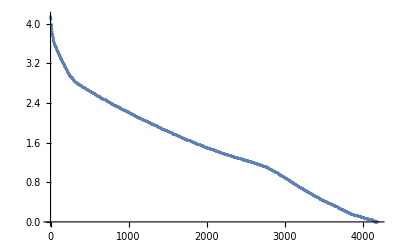

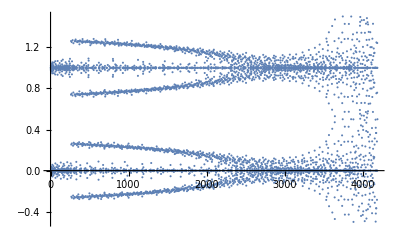

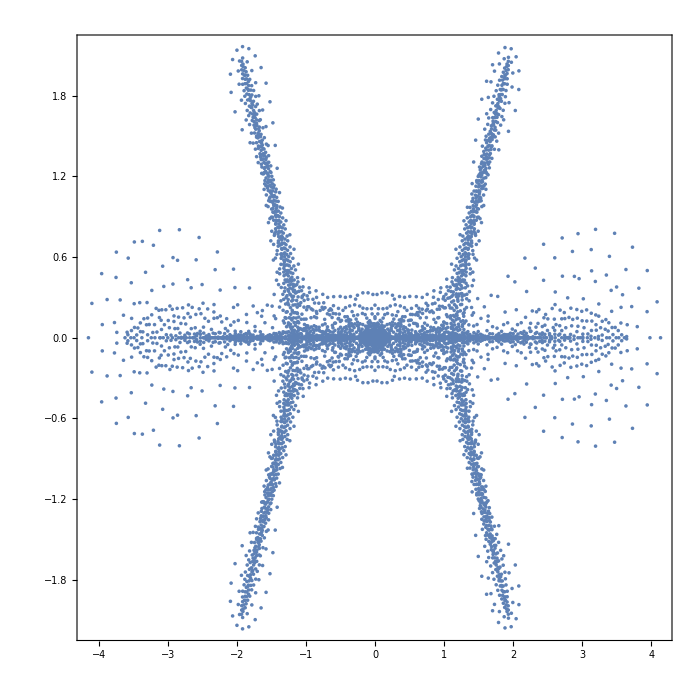

```mathematica
ν=Min[Length[ARR],Length[ARR⟦1⟧]]
λ=Eigenvalues[1.ARR⟦;;ν,;;ν⟧];
ListPlot[λ//Abs]
ListPlot[Arg[Exp[-ⅈ π/2]λ]/π+1/2]
ListPlot[Map[ReIm,λ],PlotRange->All,AspectRatio->1,Axes->False,Frame->True,ImageSize->700]
```

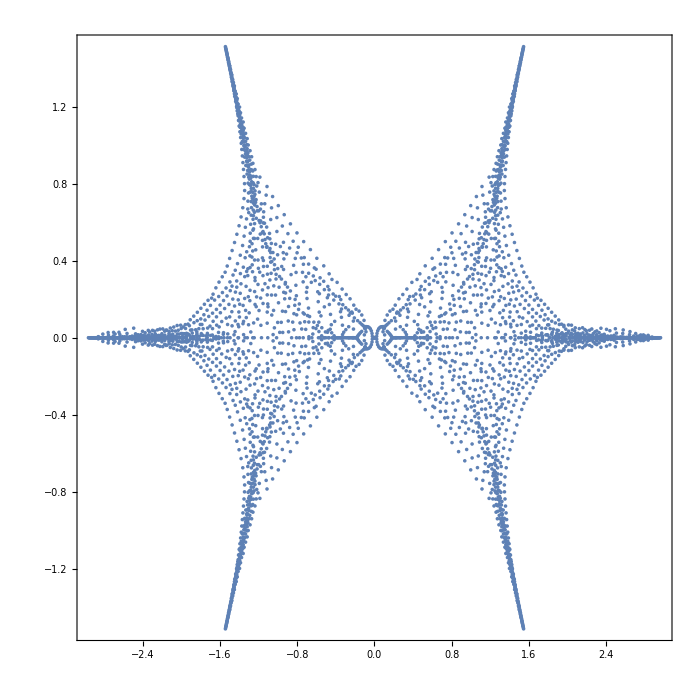

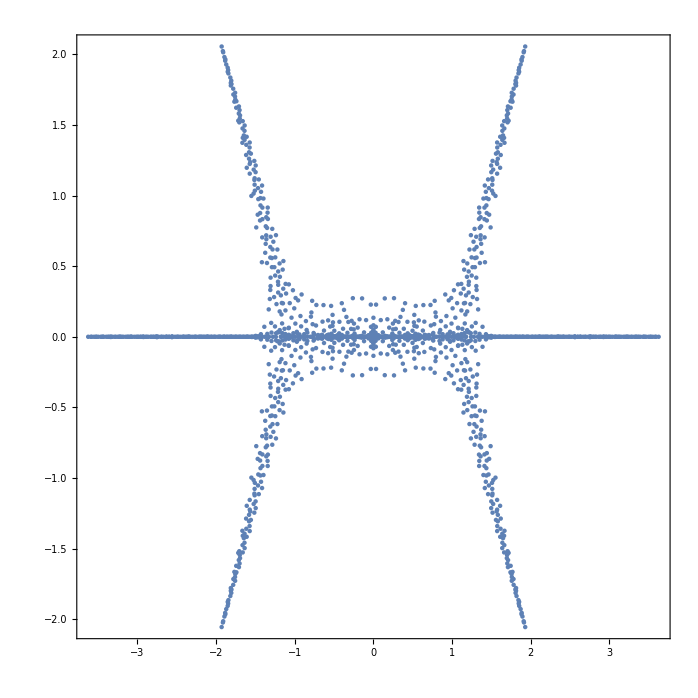

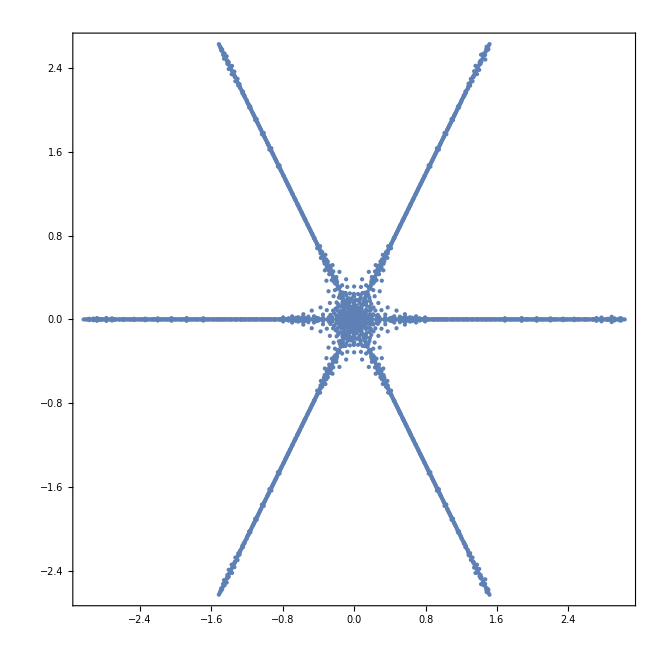

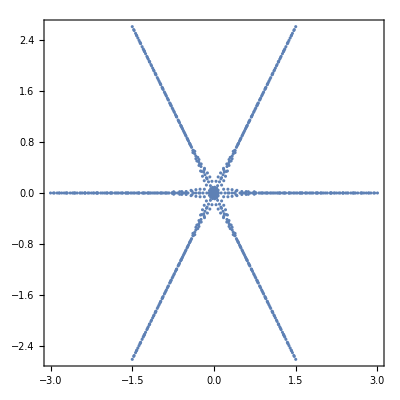

```mathematica
Eigenvalues@({{0, 1, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0}, {0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 1}, {1, 0, 0, 0, 0, 0}})//ComplexExpand
```

{-1,1,-1/2-(ⅈ √3)/2,1/2+(ⅈ √3)/2,-1/2+(ⅈ √3)/2,1/2-(ⅈ √3)/2}

## Trash

```mathematica
Clear[SmallCircle]
(* (a+b)(c+d) = ac+ad+bc+bd *)
SmallCircle[aa___,bb_Plus,cc___]:=Map[aa∘#∘cc&,bb,{1}]
(* scalars (not Ξ) don't feel ∘: (aΞ)∘(bΞ)=(ab)(Ξ∘Ξ) *)
SmallCircle[cc___,dd_?NopQ aa_,bb___]:=dd(cc∘aa∘bb)
SmallCircle[a___,0,c___]:=0
SmallCircle[a_]:=a
```

```mathematica
Ξ/:SmallCircle[cc___,Ξ[aa___],Ξ[bb___],dd___]:=cc∘Ξ[aa,bb]∘dd
```